# Infection by SARS-CoV-2 with alternate frequencies of mRNA vaccine boosting for patients undergoing antineoplastic treatment for cancer

Jeffrey P. Townsend, Hayley B. Hassler, Brinda Emu, Alex Dornburg

## SARS-CoV-2 (Gudbjartsson)

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-2 S1 IgG antibodies from Gudbjartsson et al. 2020, “Humoral Immune Response to SARS-CoV-2 in Iceland”, New England Journal of Medicine. scaled to post-BNT162b2 (Pfizer-BioNTech) booster vaccination level using the average peak value from 110 naive individuals from Kontopoulou et al. 2022 “Significant Increase in Antibody Titers after the 3rd Booster Dose of the Pfizer–BioNTech mRNA COVID-19 Vaccine in Healthcare Workers in Greece”, Vaccines.

days : 34, 48, 70, 94, 109
OD : 1.6, 1.55, 1.43, 1.19, 1.22

```mathematica
sarscov2data={
{1,34, SARSCoV2,1.6/1.6,  TRUE,NA, NA},
{2,48, SARSCoV2,1.55/1.6, FALSE, (48-34), (1.55/1.6-1.6/1.6)/(48-34)},
{3, 70, SARSCoV2,1.43/1.6,  FALSE,(70-48), (1.43/1.6-1.55/1.6)/(70-48)},
{4, 94, SARSCoV2,1.19/1.6, FALSE,(94-70),  (1.19/1.6-1.43/1.6)/(94-70)}
}
```

{{1,34,SARSCoV2,1.,TRUE,NA,NA},{2,48,SARSCoV2,0.96875,FALSE,14,-0.00223214},{3,70,SARSCoV2,0.89375,FALSE,22,-0.00340909},{4,94,SARSCoV2,0.74375,FALSE,24,-0.00625}}

### SARS-CoV-2 Waning of Antibody OD

```mathematica
sarscov2datalength=Length[sarscov2data]
```

4

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod,  0.75,1, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
sarscov2paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0.75,1.25, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.05,{}},{1.1,{}},{1.15,{}},{1.2,{}},{1.25,{}}}

Mean waning extended to targeted hormonal therapy BNT162b2-scaled peak (1.479446537) from Peeters et al 2021.

```mathematica
sarscov2meanwaningTLM={{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.0034090909090909124}},{0.95,{-0.0034090909090909124}},{1.,{-0.002232142857142857}}}
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
TableForm[sarscov2meanwaningTLM]
```

0.75 | -0.00625
0.8 | -0.00625
0.85 | -0.00625
0.9 | -0.00340909
0.95 | -0.00340909
1. | -0.00223214

```mathematica
sarscov2antibodywaningTLM=Interpolation[sarscov2meanwaningTLM]
```

InterpolatingFunction[…]

```mathematica
sarscov2antibodytimecourseTLM={1};
day=1;
While[sarscov2antibodytimecourseTLM[[day]]≥0.75,
sarscov2antibodytimecourseTLM=Append[sarscov2antibodytimecourseTLM, sarscov2antibodytimecourseTLM[[day]]+sarscov2antibodywaningTLM[sarscov2antibodytimecourseTLM[[day]]]];
sarscov2antibodytimecourseTLM=Flatten[sarscov2antibodytimecourseTLM];
Increment[day];
];
sarscov2antibodytimecourseTLM
```

{1,0.997768,0.995402,0.992906,0.990284,0.987541,0.984687,0.981728,0.978675,0.97554,0.972332,0.969064,0.965746,0.962391,0.959008,0.955607,0.952197,0.948786,0.945379,0.941982,0.938598,0.935231,0.931879,0.928545,0.925226,0.921921,0.918624,0.915332,0.912039,0.908738,0.90542,0.902076,0.898696,0.895224,0.891577,0.887733,0.883672,0.879371,0.87481,0.869969,0.864831,0.859383,0.853621,0.84755,0.841257,0.834882,0.828462,0.82203,0.815612,0.809229,0.802894,0.796617,0.790399,0.784236,0.778121,0.772038,0.76597,0.759893,0.753779,0.747592}

```mathematica
sarscov2baseline=0.1641335
```

0.164134

This baseline peak-normalized S IgG antibody level for SARS-CoV-2 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
scalarsabove1=Table[(1.422592491177772-0.422592491177772*(index-1)/(Length[sarscov2antibodytimecourseTLM]-1))/1.422592491177772, {index, Length[sarscov2antibodytimecourseTLM]}]
```

{1.,0.994965,0.98993,0.984895,0.97986,0.974826,0.969791,0.964756,0.959721,0.954686,0.949651,0.944616,0.939581,0.934547,0.929512,0.924477,0.919442,0.914407,0.909372,0.904337,0.899302,0.894267,0.889233,0.884198,0.879163,0.874128,0.869093,0.864058,0.859023,0.853988,0.848954,0.843919,0.838884,0.833849,0.828814,0.823779,0.818744,0.813709,0.808675,0.80364,0.798605,0.79357,0.788535,0.7835,0.778465,0.77343,0.768395,0.763361,0.758326,0.753291,0.748256,0.743221,0.738186,0.733151,0.728116,0.723082,0.718047,0.713012,0.707977,0.702942}

```mathematica
sarscov2antibodytimecourseBPtoExp=(sarscov2antibodytimecourseTLM+0.479446537)*scalarsabove1
```

{1.47945,1.46978,1.46,1.45011,1.44013,1.43006,1.4199,1.40968,1.39939,1.38906,1.37868,1.36829,1.35788,1.34746,1.33706,1.32667,1.31631,1.30599,1.2957,1.28545,1.27525,1.2651,1.255,1.24494,1.23494,1.22497,1.21505,1.20517,1.19532,1.18549,1.17569,1.16589,1.1561,1.14627,1.13632,1.12625,1.11605,1.10568,1.09515,1.08444,1.07355,1.06245,1.05117,1.0397,1.02812,1.01654,1.00499,0.993496,0.982076,0.970747,0.959519,0.948397,0.937382,0.926471,0.915655,0.904926,0.894267,0.883664,0.873095,0.862537}

```mathematica
Export["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv", sarscov2antibodytimecourseTLM]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

OpenWrite::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv.

$Failed

Used natural infection lambda value imputed in Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2halflife=Log[2]/ lambda /.lambda->0.0044587480795691795
```

155.458

```mathematica
Length[sarscov2antibodytimecourseBPtoExp]
```

60

```mathematica
sarscov2antibodytimecourseB=sarscov2antibodytimecourseBPtoExp;
day=Length[sarscov2antibodytimecourseB];
While[day<4393,
Increment[day];
AppendTo[sarscov2antibodytimecourseB, sarscov2baseline+(sarscov2antibodytimecourseB[[day-1]]- sarscov2baseline)*Exp[-lambda /.lambda->0.0044587480795691795]]
]
```

```mathematica
sarscov2antibodytimecourseB
```

{1.47945,1.46978,1.46,1.45011,1.44013,1.43006,1.4199,1.40968,1.39939,1.38906,1.37868,1.36829,1.35788,1.34746,1.33706,1.32667,1.31631,1.30599,1.2957,1.28545,1.27525,1.2651,1.255,1.24494,1.23494,1.22497,1.21505,1.20517,1.19532,1.18549,1.17569,1.16589,1.1561,1.14627,1.13632,1.12625,1.11605,1.10568,1.09515,1.08444,1.07355,1.06245,1.05117,1.0397,1.02812,1.01654,1.00499,0.993496,0.982076,0.970747,0.959519,0.948397,0.937382,0.926471,0.915655,0.904926,0.894267,0.883664,0.873095,0.862537,0.85943,0.856337,0.853257,0.850192,0.847139,0.844101,0.841076,0.838064,0.835066,0.832081,0.82911,0.826151,0.823206,0.820274,0.817355,0.814449,0.811556,0.808675,0.805808,0.802953,0.800111,0.797282,0.794465,0.791661,0.788869,0.78609,0.783323,0.780568,0.777826,0.775096,0.772378,0.769672,0.766978,0.764296,0.761626,0.758968,0.756321,0.753687,0.751064,0.748453,0.745853,0.743265,0.740689,0.738124,0.73557,0.733028,0.730497,0.727977,0.725469,0.722972,0.720485,0.71801,0.715546,0.713093,0.710651,0.70822,0.705799,0.703389,0.70099,0.698602,0.696224,0.693857,0.6915,0.689154,0.686818,0.684493,0.682178,0.679873,0.677579,0.675295,0.673021,0.670757,0.668503,0.666259,0.664025,0.661801,0.659587,0.657383,0.655189,0.653004,0.650829,0.648664,0.646508,0.644362,0.642226,0.640099,0.637981,0.635873,0.633775,0.631685,0.629605,0.627534,0.625473,0.62342,0.621377,0.619343,0.617318,0.615302,0.613294,0.611296,0.609307,0.607326,0.605355,0.603392,0.601438,0.599492,0.597555,0.595627,0.593707,0.591796,0.589894,0.588,0.586114,0.584237,0.582368,0.580507,0.578655,0.57681,0.574975,0.573147,0.571327,0.569516,0.567712,0.565917,0.564129,0.56235,0.560578,0.558814,0.557059,0.55531,0.55357,0.551838,0.550113,0.548396,0.546686,0.544984,0.54329,0.541603,0.539924,0.538252,0.536588,0.534931,0.533281,0.531639,0.530004,0.528376,0.526756,0.525142,0.523536,0.521937,0.520346,0.518761,0.517183,0.515613,0.514049,0.512492,0.510942,0.509399,0.507863,0.506334,0.504812,0.503296,0.501787,0.500285,0.49879,0.497301,0.495819,0.494343,0.492874,0.491412,0.489956,0.488506,0.487063,0.485626,0.484196,0.482772,0.481355,0.479943,0.478538,0.47714,0.475747,0.474361,0.472981,0.471607,0.470239,0.468877,0.467521,0.466171,0.464828,0.46349,0.462158,0.460832,0.459512,0.458198,0.45689,0.455588,0.454291,0.453,0.451715,0.450436,0.449162,0.447894,0.446631,0.445375,0.444124,0.442878,0.441638,0.440403,0.439174,0.437951,0.436732,0.43552,0.434312,0.43311,0.431914,0.430722,0.429536,0.428356,0.42718,0.42601,0.424845,0.423685,0.42253,0.421381,0.420236,0.419097,0.417963,0.416833,0.415709,0.41459,0.413476,0.412366,0.411262,0.410163,0.409068,0.407978,0.406894,0.405814,0.404738,0.403668,0.402602,0.401542,0.400485,0.399434,0.398387,0.397345,0.396307,0.395274,0.394246,0.393222,0.392203,0.391189,0.390178,0.389173,0.388172,0.387175,0.386183,0.385195,0.384211,0.383232,0.382258,0.381287,0.380321,0.379359,0.378402,0.377449,0.3765,0.375555,0.374614,0.373678,0.372746,0.371818,0.370894,0.369974,0.369058,0.368146,0.367239,0.366335,0.365436,0.36454,0.363648,0.362761,0.361877,0.360997,0.360122,0.35925,0.358382,0.357518,0.356657,0.355801,0.354948,0.354099,0.353254,0.352413,0.351575,0.350741,0.349911,0.349084,0.348262,0.347442,0.346627,0.345815,0.345007,0.344202,0.343401,0.342603,0.341809,0.341019,0.340232,0.339449,0.338669,0.337892,0.337119,0.33635,0.335583,0.334821,0.334061,0.333305,0.332553,0.331804,0.331058,0.330315,0.329576,0.32884,0.328107,0.327377,0.326651,0.325928,0.325208,0.324492,0.323778,0.323068,0.322361,0.321657,0.320956,0.320259,0.319564,0.318873,0.318184,0.317499,0.316817,0.316137,0.315461,0.314788,0.314118,0.31345,0.312786,0.312125,0.311466,0.310811,0.310158,0.309509,0.308862,0.308218,0.307577,0.306939,0.306304,0.305671,0.305041,0.304415,0.30379,0.303169,0.302551,0.301935,0.301322,0.300711,0.300104,0.299499,0.298897,0.298297,0.2977,0.297106,0.296515,0.295926,0.295339,0.294756,0.294174,0.293596,0.29302,0.292447,0.291876,0.291307,0.290742,0.290178,0.289618,0.289059,0.288504,0.28795,0.287399,0.286851,0.286305,0.285762,0.285221,0.284682,0.284146,0.283612,0.28308,0.282551,0.282024,0.2815,0.280977,0.280458,0.27994,0.279425,0.278912,0.278401,0.277893,0.277387,0.276883,0.276381,0.275882,0.275385,0.27489,0.274397,0.273907,0.273418,0.272932,0.272448,0.271966,0.271487,0.271009,0.270534,0.27006,0.269589,0.26912,0.268653,0.268188,0.267725,0.267264,0.266805,0.266348,0.265894,0.265441,0.26499,0.264542,0.264095,0.26365,0.263207,0.262767,0.262328,0.261891,0.261456,0.261023,0.260592,0.260163,0.259736,0.25931,0.258887,0.258465,0.258046,0.257628,0.257212,0.256798,0.256386,0.255975,0.255567,0.25516,0.254755,0.254352,0.25395,0.253551,0.253153,0.252757,0.252363,0.25197,0.251579,0.25119,0.250803,0.250418,0.250034,0.249652,0.249271,0.248892,0.248515,0.24814,0.247766,0.247394,0.247024,0.246655,0.246288,0.245922,0.245558,0.245196,0.244835,0.244476,0.244119,0.243763,0.243409,0.243056,0.242705,0.242356,0.242008,0.241661,0.241316,0.240973,0.240631,0.240291,0.239952,0.239615,0.239279,0.238944,0.238612,0.23828,0.23795,0.237622,0.237295,0.23697,0.236646,0.236323,0.236002,0.235682,0.235364,0.235047,0.234731,0.234417,0.234105,0.233793,0.233483,0.233175,0.232868,0.232562,0.232258,0.231955,0.231653,0.231352,0.231053,0.230756,0.230459,0.230164,0.22987,0.229578,0.229287,0.228997,0.228708,0.228421,0.228135,0.22785,0.227567,0.227285,0.227004,0.226724,0.226446,0.226168,0.225892,0.225618,0.225344,0.225072,0.224801,0.224531,0.224262,0.223995,0.223728,0.223463,0.223199,0.222936,0.222675,0.222414,0.222155,0.221897,0.22164,0.221384,0.221129,0.220876,0.220623,0.220372,0.220122,0.219873,0.219625,0.219378,0.219132,0.218888,0.218644,0.218401,0.21816,0.21792,0.21768,0.217442,0.217205,0.216969,0.216734,0.2165,0.216267,0.216035,0.215804,0.215574,0.215345,0.215118,0.214891,0.214665,0.21444,0.214216,0.213993,0.213772,0.213551,0.213331,0.213112,0.212894,0.212677,0.212461,0.212246,0.212032,0.211819,0.211607,0.211396,0.211186,0.210976,0.210768,0.21056,0.210354,0.210148,0.209943,0.20974,0.209537,0.209335,0.209134,0.208934,0.208734,0.208536,0.208338,0.208142,0.207946,0.207751,0.207557,0.207364,0.207171,0.20698,0.206789,0.206599,0.206411,0.206222,0.206035,0.205849,0.205663,0.205478,0.205295,0.205111,0.204929,0.204748,0.204567,0.204387,0.204208,0.20403,0.203852,0.203676,0.2035,0.203324,0.20315,0.202977,0.202804,0.202632,0.20246,0.20229,0.20212,0.201951,0.201783,0.201615,0.201449,0.201283,0.201117,0.200953,0.200789,0.200626,0.200464,0.200302,0.200141,0.199981,0.199821,0.199663,0.199505,0.199347,0.199191,0.199035,0.198879,0.198725,0.198571,0.198418,0.198265,0.198113,0.197962,0.197812,0.197662,0.197513,0.197364,0.197216,0.197069,0.196923,0.196777,0.196632,0.196487,0.196343,0.1962,0.196057,0.195915,0.195774,0.195633,0.195493,0.195353,0.195214,0.195076,0.194938,0.194801,0.194665,0.194529,0.194394,0.194259,0.194125,0.193992,0.193859,0.193727,0.193595,0.193464,0.193333,0.193204,0.193074,0.192946,0.192817,0.19269,0.192563,0.192436,0.19231,0.192185,0.19206,0.191936,0.191812,0.191689,0.191566,0.191444,0.191323,0.191202,0.191082,0.190962,0.190842,0.190723,0.190605,0.190487,0.19037,0.190253,0.190137,0.190022,0.189906,0.189792,0.189678,0.189564,0.189451,0.189338,0.189226,0.189114,0.189003,0.188893,0.188782,0.188673,0.188564,0.188455,0.188347,0.188239,0.188132,0.188025,0.187919,0.187813,0.187708,0.187603,0.187498,0.187394,0.187291,0.187188,0.187085,0.186983,0.186882,0.18678,0.18668,0.186579,0.186479,0.18638,0.186281,0.186183,0.186084,0.185987,0.18589,0.185793,0.185696,0.1856,0.185505,0.18541,0.185315,0.185221,0.185127,0.185034,0.184941,0.184848,0.184756,0.184664,0.184573,0.184482,0.184392,0.184301,0.184212,0.184122,0.184033,0.183945,0.183857,0.183769,0.183682,0.183595,0.183508,0.183422,0.183336,0.183251,0.183166,0.183081,0.182997,0.182913,0.182829,0.182746,0.182663,0.182581,0.182499,0.182417,0.182336,0.182255,0.182174,0.182094,0.182014,0.181934,0.181855,0.181776,0.181698,0.18162,0.181542,0.181464,0.181387,0.181311,0.181234,0.181158,0.181082,0.181007,0.180932,0.180857,0.180783,0.180709,0.180635,0.180562,0.180488,0.180416,0.180343,0.180271,0.180199,0.180128,0.180057,0.179986,0.179915,0.179845,0.179775,0.179706,0.179636,0.179567,0.179499,0.17943,0.179362,0.179295,0.179227,0.17916,0.179093,0.179027,0.17896,0.178894,0.178829,0.178763,0.178698,0.178633,0.178569,0.178505,0.178441,0.178377,0.178314,0.178251,0.178188,0.178125,0.178063,0.178001,0.177939,0.177878,0.177817,0.177756,0.177695,0.177635,0.177575,0.177515,0.177456,0.177396,0.177337,0.177279,0.17722,0.177162,0.177104,0.177046,0.176989,0.176932,0.176875,0.176818,0.176762,0.176705,0.176649,0.176594,0.176538,0.176483,0.176428,0.176374,0.176319,0.176265,0.176211,0.176157,0.176104,0.17605,0.175997,0.175945,0.175892,0.17584,0.175788,0.175736,0.175684,0.175633,0.175582,0.175531,0.17548,0.17543,0.175379,0.175329,0.175279,0.17523,0.175181,0.175131,0.175082,0.175034,0.174985,0.174937,0.174889,0.174841,0.174793,0.174746,0.174699,0.174652,0.174605,0.174558,0.174512,0.174466,0.17442,0.174374,0.174329,0.174283,0.174238,0.174193,0.174148,0.174104,0.174059,0.174015,0.173971,0.173928,0.173884,0.173841,0.173797,0.173754,0.173712,0.173669,0.173627,0.173584,0.173542,0.1735,0.173459,0.173417,0.173376,0.173335,0.173294,0.173253,0.173213,0.173172,0.173132,0.173092,0.173052,0.173012,0.172973,0.172934,0.172894,0.172855,0.172817,0.172778,0.17274,0.172701,0.172663,0.172625,0.172587,0.17255,0.172512,0.172475,0.172438,0.172401,0.172364,0.172328,0.172291,0.172255,0.172219,0.172183,0.172147,0.172111,0.172076,0.172041,0.172005,0.17197,0.171935,0.171901,0.171866,0.171832,0.171798,0.171763,0.17173,0.171696,0.171662,0.171629,0.171595,0.171562,0.171529,0.171496,0.171463,0.171431,0.171398,0.171366,0.171334,0.171302,0.17127,0.171238,0.171207,0.171175,0.171144,0.171113,0.171081,0.171051,0.17102,0.170989,0.170959,0.170928,0.170898,0.170868,0.170838,0.170808,0.170778,0.170749,0.17072,0.17069,0.170661,0.170632,0.170603,0.170574,0.170546,0.170517,0.170489,0.17046,0.170432,0.170404,0.170376,0.170349,0.170321,0.170293,0.170266,0.170239,0.170212,0.170185,0.170158,0.170131,0.170104,0.170078,0.170051,0.170025,0.169999,0.169973,0.169947,0.169921,0.169895,0.169869,0.169844,0.169818,0.169793,0.169768,0.169743,0.169718,0.169693,0.169668,0.169644,0.169619,0.169595,0.16957,0.169546,0.169522,0.169498,0.169474,0.169451,0.169427,0.169403,0.16938,0.169357,0.169333,0.16931,0.169287,0.169264,0.169241,0.169219,0.169196,0.169174,0.169151,0.169129,0.169107,0.169084,0.169062,0.169041,0.169019,0.168997,0.168975,0.168954,0.168932,0.168911,0.16889,0.168869,0.168848,0.168827,0.168806,0.168785,0.168764,0.168744,0.168723,0.168703,0.168682,0.168662,0.168642,0.168622,0.168602,0.168582,0.168562,0.168543,0.168523,0.168503,0.168484,0.168465,0.168445,0.168426,0.168407,0.168388,0.168369,0.16835,0.168332,0.168313,0.168294,0.168276,0.168257,0.168239,0.168221,0.168203,0.168184,0.168166,0.168148,0.168131,0.168113,0.168095,0.168077,0.16806,0.168042,0.168025,0.168008,0.167991,0.167973,0.167956,0.167939,0.167922,0.167905,0.167889,0.167872,0.167855,0.167839,0.167822,0.167806,0.16779,0.167773,0.167757,0.167741,0.167725,0.167709,0.167693,0.167677,0.167661,0.167646,0.16763,0.167615,0.167599,0.167584,0.167568,0.167553,0.167538,0.167523,0.167508,0.167493,0.167478,0.167463,0.167448,0.167433,0.167419,0.167404,0.167389,0.167375,0.16736,0.167346,0.167332,0.167318,0.167303,0.167289,0.167275,0.167261,0.167247,0.167234,0.16722,0.167206,0.167192,0.167179,0.167165,0.167152,0.167138,0.167125,0.167112,0.167098,0.167085,0.167072,0.167059,0.167046,0.167033,0.16702,0.167007,0.166994,0.166982,0.166969,0.166956,0.166944,0.166931,0.166919,0.166907,0.166894,0.166882,0.16687,0.166858,0.166845,0.166833,0.166821,0.166809,0.166797,0.166786,0.166774,0.166762,0.16675,0.166739,0.166727,0.166716,0.166704,0.166693,0.166681,0.16667,0.166659,0.166647,0.166636,0.166625,0.166614,0.166603,0.166592,0.166581,0.16657,0.166559,0.166549,0.166538,0.166527,0.166516,0.166506,0.166495,0.166485,0.166474,0.166464,0.166454,0.166443,0.166433,0.166423,0.166413,0.166402,0.166392,0.166382,0.166372,0.166362,0.166352,0.166343,0.166333,0.166323,0.166313,0.166303,0.166294,0.166284,0.166275,0.166265,0.166256,0.166246,0.166237,0.166227,0.166218,0.166209,0.1662,0.16619,0.166181,0.166172,0.166163,0.166154,0.166145,0.166136,0.166127,0.166118,0.16611,0.166101,0.166092,0.166083,0.166075,0.166066,0.166057,0.166049,0.16604,0.166032,0.166023,0.166015,0.166007,0.165998,0.16599,0.165982,0.165973,0.165965,0.165957,0.165949,0.165941,0.165933,0.165925,0.165917,0.165909,0.165901,0.165893,0.165885,0.165878,0.16587,0.165862,0.165854,0.165847,0.165839,0.165832,0.165824,0.165816,0.165809,0.165802,0.165794,0.165787,0.165779,0.165772,0.165765,0.165758,0.16575,0.165743,0.165736,0.165729,0.165722,0.165715,0.165708,0.165701,0.165694,0.165687,0.16568,0.165673,0.165666,0.165659,0.165652,0.165646,0.165639,0.165632,0.165626,0.165619,0.165612,0.165606,0.165599,0.165593,0.165586,0.16558,0.165573,0.165567,0.165561,0.165554,0.165548,0.165542,0.165535,0.165529,0.165523,0.165517,0.165511,0.165504,0.165498,0.165492,0.165486,0.16548,0.165474,0.165468,0.165462,0.165456,0.16545,0.165445,0.165439,0.165433,0.165427,0.165421,0.165416,0.16541,0.165404,0.165399,0.165393,0.165387,0.165382,0.165376,0.165371,0.165365,0.16536,0.165354,0.165349,0.165344,0.165338,0.165333,0.165327,0.165322,0.165317,0.165312,0.165306,0.165301,0.165296,0.165291,0.165286,0.16528,0.165275,0.16527,0.165265,0.16526,0.165255,0.16525,0.165245,0.16524,0.165235,0.16523,0.165226,0.165221,0.165216,0.165211,0.165206,0.165201,0.165197,0.165192,0.165187,0.165183,0.165178,0.165173,0.165169,0.165164,0.165159,0.165155,0.16515,0.165146,0.165141,0.165137,0.165132,0.165128,0.165124,0.165119,0.165115,0.16511,0.165106,0.165102,0.165097,0.165093,0.165089,0.165085,0.16508,0.165076,0.165072,0.165068,0.165064,0.165059,0.165055,0.165051,0.165047,0.165043,0.165039,0.165035,0.165031,0.165027,0.165023,0.165019,0.165015,0.165011,0.165007,0.165003,0.165,0.164996,0.164992,0.164988,0.164984,0.16498,0.164977,0.164973,0.164969,0.164966,0.164962,0.164958,0.164954,0.164951,0.164947,0.164944,0.16494,0.164936,0.164933,0.164929,0.164926,0.164922,0.164919,0.164915,0.164912,0.164908,0.164905,0.164901,0.164898,0.164895,0.164891,0.164888,0.164884,0.164881,0.164878,0.164874,0.164871,0.164868,0.164865,0.164861,0.164858,0.164855,0.164852,0.164848,0.164845,0.164842,0.164839,0.164836,0.164833,0.16483,0.164827,0.164823,0.16482,0.164817,0.164814,0.164811,0.164808,0.164805,0.164802,0.164799,0.164796,0.164793,0.16479,0.164787,0.164785,0.164782,0.164779,0.164776,0.164773,0.16477,0.164767,0.164765,0.164762,0.164759,0.164756,0.164753,0.164751,0.164748,0.164745,0.164742,0.16474,0.164737,0.164734,0.164732,0.164729,0.164726,0.164724,0.164721,0.164718,0.164716,0.164713,0.164711,0.164708,0.164706,0.164703,0.164701,0.164698,0.164695,0.164693,0.16469,0.164688,0.164686,0.164683,0.164681,0.164678,0.164676,0.164673,0.164671,0.164669,0.164666,0.164664,0.164661,0.164659,0.164657,0.164654,0.164652,0.16465,0.164648,0.164645,0.164643,0.164641,0.164638,0.164636,0.164634,0.164632,0.16463,0.164627,0.164625,0.164623,0.164621,0.164619,0.164616,0.164614,0.164612,0.16461,0.164608,0.164606,0.164604,0.164602,0.1646,0.164597,0.164595,0.164593,0.164591,0.164589,0.164587,0.164585,0.164583,0.164581,0.164579,0.164577,0.164575,0.164573,0.164571,0.164569,0.164567,0.164565,0.164564,0.164562,0.16456,0.164558,0.164556,0.164554,0.164552,0.16455,0.164548,0.164547,0.164545,0.164543,0.164541,0.164539,0.164538,0.164536,0.164534,0.164532,0.16453,0.164529,0.164527,0.164525,0.164523,0.164522,0.16452,0.164518,0.164516,0.164515,0.164513,0.164511,0.16451,0.164508,0.164506,0.164505,0.164503,0.164501,0.1645,0.164498,0.164497,0.164495,0.164493,0.164492,0.16449,0.164489,0.164487,0.164485,0.164484,0.164482,0.164481,0.164479,0.164478,0.164476,0.164475,0.164473,0.164472,0.16447,0.164469,0.164467,0.164466,0.164464,0.164463,0.164461,0.16446,0.164458,0.164457,0.164455,0.164454,0.164453,0.164451,0.16445,0.164448,0.164447,0.164445,0.164444,0.164443,0.164441,0.16444,0.164439,0.164437,0.164436,0.164435,0.164433,0.164432,0.164431,0.164429,0.164428,0.164427,0.164425,0.164424,0.164423,0.164421,0.16442,0.164419,0.164418,0.164416,0.164415,0.164414,0.164413,0.164411,0.16441,0.164409,0.164408,0.164406,0.164405,0.164404,0.164403,0.164402,0.1644,0.164399,0.164398,0.164397,0.164396,0.164395,0.164393,0.164392,0.164391,0.16439,0.164389,0.164388,0.164386,0.164385,0.164384,0.164383,0.164382,0.164381,0.16438,0.164379,0.164378,0.164377,0.164375,0.164374,0.164373,0.164372,0.164371,0.16437,0.164369,0.164368,0.164367,0.164366,0.164365,0.164364,0.164363,0.164362,0.164361,0.16436,0.164359,0.164358,0.164357,0.164356,0.164355,0.164354,0.164353,0.164352,0.164351,0.16435,0.164349,0.164348,0.164347,0.164346,0.164345,0.164344,0.164343,0.164342,0.164341,0.16434,0.16434,0.164339,0.164338,0.164337,0.164336,0.164335,0.164334,0.164333,0.164332,0.164331,0.164331,0.16433,0.164329,0.164328,0.164327,0.164326,0.164325,0.164325,0.164324,0.164323,0.164322,0.164321,0.16432,0.164319,0.164319,0.164318,0.164317,0.164316,0.164315,0.164315,0.164314,0.164313,0.164312,0.164311,0.164311,0.16431,0.164309,0.164308,0.164307,0.164307,0.164306,0.164305,0.164304,0.164304,0.164303,0.164302,0.164301,0.164301,0.1643,0.164299,0.164298,0.164298,0.164297,0.164296,0.164295,0.164295,0.164294,0.164293,0.164293,0.164292,0.164291,0.164291,0.16429,0.164289,0.164288,0.164288,0.164287,0.164286,0.164286,0.164285,0.164284,0.164284,0.164283,0.164282,0.164282,0.164281,0.16428,0.16428,0.164279,0.164278,0.164278,0.164277,0.164276,0.164276,0.164275,0.164275,0.164274,0.164273,0.164273,0.164272,0.164271,0.164271,0.16427,0.16427,0.164269,0.164268,0.164268,0.164267,0.164267,0.164266,0.164265,0.164265,0.164264,0.164264,0.164263,0.164263,0.164262,0.164261,0.164261,0.16426,0.16426,0.164259,0.164259,0.164258,0.164257,0.164257,0.164256,0.164256,0.164255,0.164255,0.164254,0.164254,0.164253,0.164253,0.164252,0.164252,0.164251,0.16425,0.16425,0.164249,0.164249,0.164248,0.164248,0.164247,0.164247,0.164246,0.164246,0.164245,0.164245,0.164244,0.164244,0.164243,0.164243,0.164242,0.164242,0.164241,0.164241,0.16424,0.16424,0.16424,0.164239,0.164239,0.164238,0.164238,0.164237,0.164237,0.164236,0.164236,0.164235,0.164235,0.164234,0.164234,0.164234,0.164233,0.164233,0.164232,0.164232,0.164231,0.164231,0.164231,0.16423,0.16423,0.164229,0.164229,0.164228,0.164228,0.164228,0.164227,0.164227,0.164226,0.164226,0.164225,0.164225,0.164225,0.164224,0.164224,0.164223,0.164223,0.164223,0.164222,0.164222,0.164221,0.164221,0.164221,0.16422,0.16422,0.164219,0.164219,0.164219,0.164218,0.164218,0.164218,0.164217,0.164217,0.164216,0.164216,0.164216,0.164215,0.164215,0.164215,0.164214,0.164214,0.164214,0.164213,0.164213,0.164213,0.164212,0.164212,0.164211,0.164211,0.164211,0.16421,0.16421,0.16421,0.164209,0.164209,0.164209,0.164208,0.164208,0.164208,0.164207,0.164207,0.164207,0.164206,0.164206,0.164206,0.164205,0.164205,0.164205,0.164204,0.164204,0.164204,0.164204,0.164203,0.164203,0.164203,0.164202,0.164202,0.164202,0.164201,0.164201,0.164201,0.1642,0.1642,0.1642,0.1642,0.164199,0.164199,0.164199,0.164198,0.164198,0.164198,0.164198,0.164197,0.164197,0.164197,0.164196,0.164196,0.164196,0.164196,0.164195,0.164195,0.164195,0.164195,0.164194,0.164194,0.164194,0.164193,0.164193,0.164193,0.164193,0.164192,0.164192,0.164192,0.164192,0.164191,0.164191,0.164191,0.164191,0.16419,0.16419,0.16419,0.16419,0.164189,0.164189,0.164189,0.164189,0.164188,0.164188,0.164188,0.164188,0.164187,0.164187,0.164187,0.164187,0.164186,0.164186,0.164186,0.164186,0.164185,0.164185,0.164185,0.164185,0.164185,0.164184,0.164184,0.164184,0.164184,0.164183,0.164183,0.164183,0.164183,0.164183,0.164182,0.164182,0.164182,0.164182,0.164181,0.164181,0.164181,0.164181,0.164181,0.16418,0.16418,0.16418,0.16418,0.16418,0.164179,0.164179,0.164179,0.164179,0.164179,0.164178,0.164178,0.164178,0.164178,0.164178,0.164177,0.164177,0.164177,0.164177,0.164177,0.164176,0.164176,0.164176,0.164176,0.164176,0.164175,0.164175,0.164175,0.164175,0.164175,0.164175,0.164174,0.164174,0.164174,0.164174,0.164174,0.164173,0.164173,0.164173,0.164173,0.164173,0.164173,0.164172,0.164172,0.164172,0.164172,0.164172,0.164172,0.164171,0.164171,0.164171,0.164171,0.164171,0.164171,0.16417,0.16417,0.16417,0.16417,0.16417,0.16417,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134}

```mathematica
sarscov2antibodytimecourseB[[150]]
```

0.631685

```mathematica
1.675000077*(10^3.02)/(10^3.373)
```

0.743045

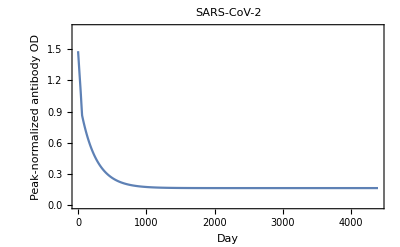

```mathematica
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster04May2023.pdf.

$Failed

### SARS-CoV-2 Probability of Infection | Antibody OD

```mathematica
sarscov2probinfgivenaod[aod_]:=1/(1+Exp[-(-5.841733+-5.323444*aod)])
```

These values for a and b come from the ancestral and descendent states natural infection analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2probinfgivenaod[aod]
```

1/(1+ⅇ^(5.84173+5.32344 aod))

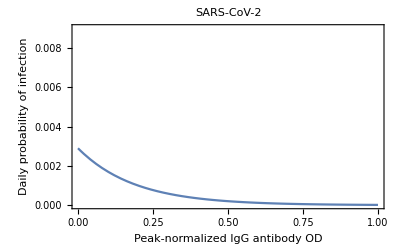

```mathematica
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster04May2023.pdf.

$Failed

```mathematica
sarscov2probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

### SARS-CoV-2 Probability of No Reinfection Time Course

```mathematica
sarscov2probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov2probnoreinfectiontimecourse, 
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov2probnoreinfectiontimecourse, 
If[day<Length[sarscov2antibodytimecourseB],
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]] ]),
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]])
]
]
];

sarscov2probnoreinfectiontimecourse
```

{1,0.999999,0.999998,0.999996,0.999995,0.999994,0.999992,0.99999,0.999989,0.999987,0.999985,0.999983,0.999981,0.999979,0.999976,0.999974,0.999971,0.999968,0.999966,0.999962,0.999959,0.999956,0.999952,0.999948,0.999944,0.99994,0.999935,0.999931,0.999926,0.99992,0.999915,0.999909,0.999903,0.999896,0.999889,0.999882,0.999875,0.999867,0.999858,0.999849,0.999839,0.999829,0.999818,0.999807,0.999795,0.999782,0.999768,0.999753,0.999738,0.999721,0.999704,0.999685,0.999665,0.999644,0.999622,0.999599,0.999574,0.999548,0.99952,0.99949,0.99946,0.99943,0.999399,0.999368,0.999336,0.999303,0.99927,0.999237,0.999203,0.999168,0.999133,0.999097,0.999061,0.999024,0.998987,0.998949,0.99891,0.998871,0.998832,0.998791,0.99875,0.998709,0.998666,0.998623,0.99858,0.998536,0.998491,0.998446,0.998399,0.998353,0.998305,0.998257,0.998208,0.998159,0.998108,0.998057,0.998006,0.997953,0.9979,0.997846,0.997791,0.997736,0.99768,0.997623,0.997565,0.997507,0.997447,0.997387,0.997326,0.997265,0.997202,0.997139,0.997075,0.99701,0.996944,0.996877,0.996809,0.996741,0.996672,0.996602,0.99653,0.996458,0.996386,0.996312,0.996237,0.996161,0.996085,0.996007,0.995929,0.995849,0.995769,0.995688,0.995605,0.995522,0.995438,0.995352,0.995266,0.995179,0.995091,0.995001,0.994911,0.994819,0.994727,0.994633,0.994539,0.994443,0.994346,0.994249,0.99415,0.99405,0.993949,0.993846,0.993743,0.993639,0.993533,0.993426,0.993319,0.99321,0.993099,0.992988,0.992876,0.992762,0.992647,0.992531,0.992414,0.992295,0.992175,0.992055,0.991932,0.991809,0.991684,0.991559,0.991431,0.991303,0.991173,0.991043,0.99091,0.990777,0.990642,0.990506,0.990369,0.99023,0.99009,0.989949,0.989806,0.989662,0.989517,0.98937,0.989222,0.989073,0.988922,0.98877,0.988616,0.988461,0.988305,0.988147,0.987988,0.987828,0.987666,0.987502,0.987338,0.987171,0.987004,0.986835,0.986664,0.986492,0.986319,0.986144,0.985968,0.98579,0.98561,0.98543,0.985247,0.985063,0.984878,0.984691,0.984503,0.984313,0.984122,0.983929,0.983734,0.983538,0.983341,0.983142,0.982941,0.982739,0.982535,0.98233,0.982123,0.981915,0.981705,0.981493,0.98128,0.981065,0.980849,0.980631,0.980412,0.98019,0.979968,0.979743,0.979517,0.97929,0.979061,0.97883,0.978597,0.978363,0.978127,0.97789,0.977651,0.97741,0.977168,0.976924,0.976678,0.976431,0.976182,0.975931,0.975679,0.975425,0.975169,0.974912,0.974653,0.974392,0.974129,0.973865,0.9736,0.973332,0.973063,0.972792,0.972519,0.972245,0.971969,0.971691,0.971412,0.971131,0.970848,0.970563,0.970277,0.969989,0.969699,0.969408,0.969115,0.96882,0.968523,0.968225,0.967925,0.967623,0.967319,0.967014,0.966707,0.966398,0.966088,0.965776,0.965462,0.965146,0.964828,0.964509,0.964188,0.963866,0.963541,0.963215,0.962887,0.962558,0.962226,0.961893,0.961558,0.961222,0.960883,0.960543,0.960201,0.959858,0.959512,0.959165,0.958816,0.958466,0.958113,0.957759,0.957403,0.957046,0.956687,0.956325,0.955963,0.955598,0.955232,0.954864,0.954494,0.954123,0.953749,0.953375,0.952998,0.952619,0.952239,0.951857,0.951474,0.951088,0.950701,0.950313,0.949922,0.94953,0.949136,0.94874,0.948343,0.947944,0.947543,0.947141,0.946736,0.94633,0.945923,0.945513,0.945102,0.94469,0.944275,0.943859,0.943441,0.943022,0.942601,0.942178,0.941753,0.941327,0.940899,0.94047,0.940038,0.939605,0.939171,0.938735,0.938297,0.937857,0.937416,0.936973,0.936528,0.936082,0.935634,0.935185,0.934734,0.934281,0.933827,0.933371,0.932913,0.932454,0.931993,0.931531,0.931067,0.930601,0.930134,0.929665,0.929195,0.928723,0.928249,0.927774,0.927297,0.926819,0.926339,0.925857,0.925374,0.924889,0.924403,0.923916,0.923426,0.922935,0.922443,0.921949,0.921454,0.920957,0.920458,0.919958,0.919457,0.918954,0.918449,0.917943,0.917436,0.916927,0.916416,0.915904,0.915391,0.914876,0.914359,0.913842,0.913322,0.912802,0.912279,0.911756,0.911231,0.910704,0.910176,0.909647,0.909116,0.908584,0.90805,0.907515,0.906978,0.906441,0.905901,0.905361,0.904819,0.904275,0.903731,0.903184,0.902637,0.902088,0.901538,0.900986,0.900434,0.899879,0.899324,0.898767,0.898209,0.897649,0.897089,0.896526,0.895963,0.895398,0.894832,0.894265,0.893697,0.893127,0.892556,0.891983,0.89141,0.890835,0.890259,0.889682,0.889103,0.888524,0.887943,0.88736,0.886777,0.886192,0.885607,0.88502,0.884431,0.883842,0.883252,0.88266,0.882067,0.881473,0.880878,0.880282,0.879684,0.879086,0.878486,0.877885,0.877283,0.87668,0.876076,0.875471,0.874864,0.874257,0.873648,0.873039,0.872428,0.871817,0.871204,0.87059,0.869975,0.869359,0.868742,0.868124,0.867505,0.866885,0.866264,0.865642,0.865019,0.864395,0.86377,0.863144,0.862517,0.861889,0.86126,0.86063,0.859999,0.859368,0.858735,0.858101,0.857467,0.856831,0.856195,0.855557,0.854919,0.85428,0.85364,0.852999,0.852357,0.851715,0.851071,0.850427,0.849782,0.849135,0.848488,0.847841,0.847192,0.846543,0.845892,0.845241,0.844589,0.843937,0.843283,0.842629,0.841974,0.841318,0.840661,0.840004,0.839345,0.838687,0.838027,0.837366,0.836705,0.836043,0.835381,0.834717,0.834053,0.833388,0.832723,0.832057,0.83139,0.830722,0.830054,0.829385,0.828715,0.828045,0.827374,0.826702,0.82603,0.825357,0.824684,0.82401,0.823335,0.822659,0.821983,0.821307,0.820629,0.819952,0.819273,0.818594,0.817914,0.817234,0.816553,0.815872,0.81519,0.814508,0.813825,0.813141,0.812457,0.811773,0.811088,0.810402,0.809716,0.809029,0.808342,0.807654,0.806966,0.806277,0.805588,0.804899,0.804209,0.803518,0.802827,0.802135,0.801444,0.800751,0.800058,0.799365,0.798671,0.797977,0.797283,0.796588,0.795892,0.795197,0.794501,0.793804,0.793107,0.79241,0.791712,0.791014,0.790315,0.789617,0.788917,0.788218,0.787518,0.786818,0.786117,0.785416,0.784715,0.784014,0.783312,0.78261,0.781907,0.781204,0.780501,0.779798,0.779094,0.77839,0.777686,0.776982,0.776277,0.775572,0.774866,0.774161,0.773455,0.772749,0.772043,0.771336,0.770629,0.769922,0.769215,0.768508,0.7678,0.767092,0.766384,0.765676,0.764967,0.764259,0.76355,0.762841,0.762132,0.761422,0.760713,0.760003,0.759293,0.758583,0.757873,0.757163,0.756452,0.755742,0.755031,0.75432,0.753609,0.752898,0.752187,0.751475,0.750764,0.750052,0.749341,0.748629,0.747917,0.747205,0.746493,0.745781,0.745069,0.744357,0.743644,0.742932,0.742219,0.741507,0.740794,0.740082,0.739369,0.738657,0.737944,0.737231,0.736518,0.735806,0.735093,0.73438,0.733667,0.732954,0.732242,0.731529,0.730816,0.730103,0.72939,0.728677,0.727965,0.727252,0.726539,0.725826,0.725114,0.724401,0.723688,0.722976,0.722263,0.721551,0.720838,0.720126,0.719414,0.718702,0.717989,0.717277,0.716565,0.715853,0.715142,0.71443,0.713718,0.713007,0.712295,0.711584,0.710872,0.710161,0.70945,0.708739,0.708028,0.707318,0.706607,0.705897,0.705186,0.704476,0.703766,0.703056,0.702346,0.701636,0.700927,0.700218,0.699508,0.698799,0.69809,0.697382,0.696673,0.695965,0.695256,0.694548,0.693841,0.693133,0.692425,0.691718,0.691011,0.690304,0.689597,0.688891,0.688184,0.687478,0.686772,0.686066,0.685361,0.684655,0.68395,0.683245,0.682541,0.681836,0.681132,0.680428,0.679724,0.679021,0.678318,0.677615,0.676912,0.676209,0.675507,0.674805,0.674103,0.673402,0.6727,0.671999,0.671299,0.670598,0.669898,0.669198,0.668498,0.667799,0.6671,0.666401,0.665702,0.665004,0.664306,0.663608,0.662911,0.662214,0.661517,0.660821,0.660124,0.659429,0.658733,0.658038,0.657343,0.656648,0.655954,0.65526,0.654566,0.653873,0.653179,0.652487,0.651794,0.651102,0.65041,0.649719,0.649028,0.648337,0.647647,0.646957,0.646267,0.645578,0.644889,0.6442,0.643512,0.642824,0.642136,0.641449,0.640762,0.640075,0.639389,0.638703,0.638018,0.637333,0.636648,0.635964,0.63528,0.634596,0.633913,0.63323,0.632548,0.631866,0.631184,0.630503,0.629822,0.629141,0.628461,0.627781,0.627102,0.626423,0.625744,0.625066,0.624389,0.623711,0.623034,0.622358,0.621682,0.621006,0.620331,0.619656,0.618981,0.618307,0.617634,0.61696,0.616288,0.615615,0.614943,0.614272,0.613601,0.61293,0.61226,0.61159,0.61092,0.610251,0.609583,0.608915,0.608247,0.60758,0.606913,0.606247,0.605581,0.604916,0.604251,0.603586,0.602922,0.602258,0.601595,0.600932,0.60027,0.599608,0.598947,0.598286,0.597625,0.596965,0.596306,0.595647,0.594988,0.59433,0.593672,0.593015,0.592358,0.591702,0.591046,0.590391,0.589736,0.589081,0.588427,0.587774,0.587121,0.586468,0.585816,0.585165,0.584513,0.583863,0.583213,0.582563,0.581914,0.581265,0.580617,0.579969,0.579322,0.578675,0.578029,0.577383,0.576738,0.576093,0.575449,0.574805,0.574162,0.573519,0.572877,0.572235,0.571594,0.570953,0.570313,0.569673,0.569034,0.568395,0.567756,0.567119,0.566481,0.565845,0.565208,0.564572,0.563937,0.563302,0.562668,0.562034,0.561401,0.560769,0.560136,0.559505,0.558873,0.558243,0.557613,0.556983,0.556354,0.555725,0.555097,0.55447,0.553843,0.553216,0.55259,0.551965,0.55134,0.550715,0.550091,0.549468,0.548845,0.548223,0.547601,0.54698,0.546359,0.545739,0.545119,0.5445,0.543881,0.543263,0.542645,0.542028,0.541412,0.540796,0.54018,0.539565,0.538951,0.538337,0.537724,0.537111,0.536498,0.535887,0.535275,0.534665,0.534055,0.533445,0.532836,0.532227,0.531619,0.531012,0.530405,0.529799,0.529193,0.528588,0.527983,0.527379,0.526775,0.526172,0.525569,0.524967,0.524366,0.523765,0.523164,0.522564,0.521965,0.521366,0.520768,0.52017,0.519573,0.518976,0.51838,0.517785,0.51719,0.516595,0.516001,0.515408,0.514815,0.514223,0.513631,0.51304,0.51245,0.511859,0.51127,0.510681,0.510093,0.509505,0.508917,0.508331,0.507744,0.507159,0.506574,0.505989,0.505405,0.504822,0.504239,0.503656,0.503074,0.502493,0.501912,0.501332,0.500753,0.500174,0.499595,0.499017,0.49844,0.497863,0.497287,0.496711,0.496136,0.495561,0.494987,0.494413,0.49384,0.493268,0.492696,0.492125,0.491554,0.490984,0.490414,0.489845,0.489276,0.488708,0.488141,0.487574,0.487008,0.486442,0.485877,0.485312,0.484748,0.484184,0.483621,0.483059,0.482497,0.481936,0.481375,0.480815,0.480255,0.479696,0.479137,0.478579,0.478022,0.477465,0.476908,0.476353,0.475797,0.475243,0.474688,0.474135,0.473582,0.473029,0.472477,0.471926,0.471375,0.470825,0.470275,0.469726,0.469177,0.468629,0.468082,0.467535,0.466988,0.466443,0.465897,0.465353,0.464808,0.464265,0.463722,0.463179,0.462637,0.462096,0.461555,0.461014,0.460475,0.459935,0.459397,0.458859,0.458321,0.457784,0.457248,0.456712,0.456176,0.455642,0.455107,0.454574,0.454041,0.453508,0.452976,0.452444,0.451913,0.451383,0.450853,0.450324,0.449795,0.449267,0.448739,0.448212,0.447686,0.44716,0.446634,0.446109,0.445585,0.445061,0.444538,0.444015,0.443493,0.442971,0.44245,0.44193,0.44141,0.44089,0.440371,0.439853,0.439335,0.438818,0.438301,0.437785,0.437269,0.436754,0.43624,0.435726,0.435212,0.434699,0.434187,0.433675,0.433164,0.432653,0.432143,0.431633,0.431124,0.430616,0.430108,0.4296,0.429093,0.428587,0.428081,0.427576,0.427071,0.426567,0.426063,0.42556,0.425057,0.424555,0.424053,0.423552,0.423052,0.422552,0.422053,0.421554,0.421055,0.420558,0.42006,0.419564,0.419068,0.418572,0.418077,0.417582,0.417088,0.416595,0.416102,0.415609,0.415117,0.414626,0.414135,0.413645,0.413155,0.412666,0.412177,0.411689,0.411201,0.410714,0.410228,0.409742,0.409256,0.408771,0.408287,0.407803,0.407319,0.406836,0.406354,0.405872,0.405391,0.40491,0.40443,0.40395,0.403471,0.402992,0.402514,0.402036,0.401559,0.401083,0.400607,0.400131,0.399656,0.399182,0.398708,0.398234,0.397761,0.397289,0.396817,0.396346,0.395875,0.395405,0.394935,0.394466,0.393997,0.393529,0.393061,0.392594,0.392127,0.391661,0.391195,0.39073,0.390265,0.389801,0.389338,0.388875,0.388412,0.38795,0.387489,0.387028,0.386567,0.386107,0.385648,0.385189,0.38473,0.384272,0.383815,0.383358,0.382901,0.382446,0.38199,0.381535,0.381081,0.380627,0.380174,0.379721,0.379269,0.378817,0.378365,0.377915,0.377464,0.377014,0.376565,0.376116,0.375668,0.37522,0.374773,0.374326,0.37388,0.373434,0.372989,0.372544,0.3721,0.371656,0.371213,0.37077,0.370327,0.369886,0.369444,0.369004,0.368563,0.368124,0.367684,0.367245,0.366807,0.366369,0.365932,0.365495,0.365059,0.364623,0.364188,0.363753,0.363318,0.362885,0.362451,0.362018,0.361586,0.361154,0.360723,0.360292,0.359861,0.359431,0.359002,0.358573,0.358144,0.357717,0.357289,0.356862,0.356435,0.356009,0.355584,0.355159,0.354734,0.35431,0.353886,0.353463,0.353041,0.352619,0.352197,0.351776,0.351355,0.350935,0.350515,0.350096,0.349677,0.349258,0.348841,0.348423,0.348006,0.34759,0.347174,0.346759,0.346344,0.345929,0.345515,0.345101,0.344688,0.344276,0.343864,0.343452,0.343041,0.34263,0.34222,0.34181,0.341401,0.340992,0.340583,0.340176,0.339768,0.339361,0.338955,0.338549,0.338143,0.337738,0.337333,0.336929,0.336526,0.336122,0.33572,0.335317,0.334915,0.334514,0.334113,0.333713,0.333313,0.332913,0.332514,0.332116,0.331717,0.33132,0.330922,0.330526,0.330129,0.329734,0.329338,0.328943,0.328549,0.328155,0.327761,0.327368,0.326975,0.326583,0.326192,0.3258,0.325409,0.325019,0.324629,0.32424,0.323851,0.323462,0.323074,0.322686,0.322299,0.321912,0.321526,0.32114,0.320755,0.32037,0.319985,0.319601,0.319217,0.318834,0.318452,0.318069,0.317687,0.317306,0.316925,0.316545,0.316164,0.315785,0.315406,0.315027,0.314649,0.314271,0.313893,0.313516,0.31314,0.312764,0.312388,0.312013,0.311638,0.311264,0.31089,0.310516,0.310143,0.309771,0.309398,0.309027,0.308655,0.308284,0.307914,0.307544,0.307174,0.306805,0.306437,0.306068,0.3057,0.305333,0.304966,0.304599,0.304233,0.303868,0.303502,0.303138,0.302773,0.302409,0.302046,0.301682,0.30132,0.300957,0.300596,0.300234,0.299873,0.299512,0.299152,0.298793,0.298433,0.298074,0.297716,0.297358,0.297,0.296643,0.296286,0.29593,0.295574,0.295218,0.294863,0.294508,0.294154,0.2938,0.293447,0.293094,0.292741,0.292389,0.292037,0.291686,0.291335,0.290984,0.290634,0.290284,0.289935,0.289586,0.289238,0.288889,0.288542,0.288194,0.287848,0.287501,0.287155,0.286809,0.286464,0.286119,0.285775,0.285431,0.285087,0.284744,0.284401,0.284059,0.283717,0.283375,0.283034,0.282693,0.282353,0.282013,0.281673,0.281334,0.280996,0.280657,0.280319,0.279982,0.279644,0.279308,0.278971,0.278635,0.2783,0.277965,0.27763,0.277295,0.276961,0.276628,0.276294,0.275962,0.275629,0.275297,0.274966,0.274634,0.274303,0.273973,0.273643,0.273313,0.272984,0.272655,0.272327,0.271998,0.271671,0.271343,0.271016,0.27069,0.270364,0.270038,0.269712,0.269387,0.269063,0.268738,0.268415,0.268091,0.267768,0.267445,0.267123,0.266801,0.266479,0.266158,0.265837,0.265517,0.265197,0.264877,0.264558,0.264239,0.263921,0.263602,0.263285,0.262967,0.26265,0.262333,0.262017,0.261701,0.261386,0.261071,0.260756,0.260441,0.260127,0.259814,0.259501,0.259188,0.258875,0.258563,0.258251,0.25794,0.257629,0.257318,0.257008,0.256698,0.256388,0.256079,0.25577,0.255462,0.255154,0.254846,0.254538,0.254231,0.253925,0.253618,0.253313,0.253007,0.252702,0.252397,0.252093,0.251788,0.251485,0.251181,0.250878,0.250576,0.250273,0.249971,0.24967,0.249369,0.249068,0.248767,0.248467,0.248167,0.247868,0.247569,0.24727,0.246972,0.246674,0.246376,0.246079,0.245782,0.245485,0.245189,0.244893,0.244598,0.244303,0.244008,0.243713,0.243419,0.243126,0.242832,0.242539,0.242246,0.241954,0.241662,0.24137,0.241079,0.240788,0.240497,0.240207,0.239917,0.239628,0.239338,0.23905,0.238761,0.238473,0.238185,0.237897,0.23761,0.237323,0.237037,0.236751,0.236465,0.23618,0.235894,0.23561,0.235325,0.235041,0.234757,0.234474,0.234191,0.233908,0.233626,0.233344,0.233062,0.232781,0.2325,0.232219,0.231938,0.231658,0.231379,0.231099,0.23082,0.230542,0.230263,0.229985,0.229707,0.22943,0.229153,0.228876,0.2286,0.228324,0.228048,0.227773,0.227498,0.227223,0.226949,0.226675,0.226401,0.226127,0.225854,0.225581,0.225309,0.225037,0.224765,0.224494,0.224223,0.223952,0.223681,0.223411,0.223141,0.222872,0.222603,0.222334,0.222065,0.221797,0.221529,0.221261,0.220994,0.220727,0.220461,0.220194,0.219928,0.219663,0.219397,0.219132,0.218868,0.218603,0.218339,0.218075,0.217812,0.217549,0.217286,0.217023,0.216761,0.216499,0.216238,0.215977,0.215716,0.215455,0.215195,0.214935,0.214675,0.214416,0.214157,0.213898,0.213639,0.213381,0.213124,0.212866,0.212609,0.212352,0.212095,0.211839,0.211583,0.211327,0.211072,0.210817,0.210562,0.210308,0.210054,0.2098,0.209546,0.209293,0.20904,0.208788,0.208535,0.208283,0.208032,0.20778,0.207529,0.207278,0.207028,0.206778,0.206528,0.206278,0.206029,0.20578,0.205531,0.205283,0.205035,0.204787,0.20454,0.204292,0.204045,0.203799,0.203553,0.203307,0.203061,0.202815,0.20257,0.202325,0.202081,0.201837,0.201593,0.201349,0.201106,0.200863,0.20062,0.200377,0.200135,0.199893,0.199652,0.19941,0.199169,0.198929,0.198688,0.198448,0.198208,0.197968,0.197729,0.19749,0.197251,0.197013,0.196775,0.196537,0.196299,0.196062,0.195825,0.195588,0.195352,0.195116,0.19488,0.194644,0.194409,0.194174,0.193939,0.193705,0.193471,0.193237,0.193003,0.19277,0.192537,0.192304,0.192071,0.191839,0.191607,0.191376,0.191144,0.190913,0.190682,0.190452,0.190222,0.189992,0.189762,0.189532,0.189303,0.189074,0.188846,0.188617,0.188389,0.188162,0.187934,0.187707,0.18748,0.187253,0.187027,0.186801,0.186575,0.186349,0.186124,0.185899,0.185674,0.18545,0.185225,0.185001,0.184778,0.184554,0.184331,0.184108,0.183886,0.183663,0.183441,0.183219,0.182998,0.182777,0.182555,0.182335,0.182114,0.181894,0.181674,0.181454,0.181235,0.181016,0.180797,0.180578,0.18036,0.180142,0.179924,0.179706,0.179489,0.179272,0.179055,0.178839,0.178622,0.178406,0.178191,0.177975,0.17776,0.177545,0.17733,0.177116,0.176902,0.176688,0.176474,0.17626,0.176047,0.175834,0.175622,0.175409,0.175197,0.174985,0.174774,0.174562,0.174351,0.17414,0.17393,0.173719,0.173509,0.173299,0.17309,0.17288,0.172671,0.172463,0.172254,0.172046,0.171838,0.17163,0.171422,0.171215,0.171008,0.170801,0.170594,0.170388,0.170182,0.169976,0.16977,0.169565,0.16936,0.169155,0.16895,0.168746,0.168542,0.168338,0.168135,0.167931,0.167728,0.167525,0.167323,0.16712,0.166918,0.166716,0.166514,0.166313,0.166112,0.165911,0.16571,0.16551,0.16531,0.16511,0.16491,0.16471,0.164511,0.164312,0.164113,0.163915,0.163717,0.163519,0.163321,0.163123,0.162926,0.162729,0.162532,0.162335,0.162139,0.161943,0.161747,0.161551,0.161356,0.161161,0.160966,0.160771,0.160576,0.160382,0.160188,0.159994,0.159801,0.159608,0.159414,0.159222,0.159029,0.158837,0.158644,0.158453,0.158261,0.158069,0.157878,0.157687,0.157496,0.157306,0.157116,0.156925,0.156736,0.156546,0.156357,0.156167,0.155979,0.15579,0.155601,0.155413,0.155225,0.155037,0.15485,0.154662,0.154475,0.154288,0.154102,0.153915,0.153729,0.153543,0.153357,0.153172,0.152986,0.152801,0.152616,0.152432,0.152247,0.152063,0.151879,0.151695,0.151512,0.151329,0.151146,0.150963,0.15078,0.150598,0.150415,0.150233,0.150052,0.14987,0.149689,0.149508,0.149327,0.149146,0.148966,0.148785,0.148605,0.148426,0.148246,0.148067,0.147887,0.147709,0.14753,0.147351,0.147173,0.146995,0.146817,0.146639,0.146462,0.146285,0.146108,0.145931,0.145754,0.145578,0.145402,0.145226,0.14505,0.144875,0.1447,0.144524,0.14435,0.144175,0.144,0.143826,0.143652,0.143478,0.143305,0.143131,0.142958,0.142785,0.142612,0.14244,0.142268,0.142095,0.141923,0.141752,0.14158,0.141409,0.141238,0.141067,0.140896,0.140726,0.140555,0.140385,0.140215,0.140046,0.139876,0.139707,0.139538,0.139369,0.139201,0.139032,0.138864,0.138696,0.138528,0.13836,0.138193,0.138026,0.137859,0.137692,0.137525,0.137359,0.137193,0.137027,0.136861,0.136695,0.13653,0.136365,0.1362,0.136035,0.13587,0.135706,0.135541,0.135377,0.135214,0.13505,0.134887,0.134723,0.13456,0.134398,0.134235,0.134072,0.13391,0.133748,0.133586,0.133425,0.133263,0.133102,0.132941,0.13278,0.132619,0.132459,0.132299,0.132138,0.131979,0.131819,0.131659,0.1315,0.131341,0.131182,0.131023,0.130865,0.130706,0.130548,0.13039,0.130232,0.130075,0.129917,0.12976,0.129603,0.129446,0.12929,0.129133,0.128977,0.128821,0.128665,0.128509,0.128354,0.128198,0.128043,0.127888,0.127733,0.127579,0.127424,0.12727,0.127116,0.126962,0.126809,0.126655,0.126502,0.126349,0.126196,0.126043,0.125891,0.125738,0.125586,0.125434,0.125282,0.125131,0.124979,0.124828,0.124677,0.124526,0.124375,0.124225,0.124075,0.123924,0.123774,0.123625,0.123475,0.123326,0.123176,0.123027,0.122878,0.12273,0.122581,0.122433,0.122285,0.122137,0.121989,0.121841,0.121694,0.121546,0.121399,0.121252,0.121106,0.120959,0.120813,0.120667,0.12052,0.120375,0.120229,0.120083,0.119938,0.119793,0.119648,0.119503,0.119359,0.119214,0.11907,0.118926,0.118782,0.118638,0.118494,0.118351,0.118208,0.118065,0.117922,0.117779,0.117637,0.117494,0.117352,0.11721,0.117068,0.116926,0.116785,0.116644,0.116502,0.116361,0.116221,0.11608,0.115939,0.115799,0.115659,0.115519,0.115379,0.11524,0.1151,0.114961,0.114822,0.114683,0.114544,0.114405,0.114267,0.114128,0.11399,0.113852,0.113715,0.113577,0.113439,0.113302,0.113165,0.113028,0.112891,0.112755,0.112618,0.112482,0.112346,0.11221,0.112074,0.111938,0.111803,0.111667,0.111532,0.111397,0.111263,0.111128,0.110993,0.110859,0.110725,0.110591,0.110457,0.110323,0.11019,0.110056,0.109923,0.10979,0.109657,0.109525,0.109392,0.10926,0.109127,0.108995,0.108863,0.108732,0.1086,0.108469,0.108337,0.108206,0.108075,0.107944,0.107814,0.107683,0.107553,0.107423,0.107293,0.107163,0.107033,0.106904,0.106774,0.106645,0.106516,0.106387,0.106258,0.10613,0.106001,0.105873,0.105745,0.105617,0.105489,0.105361,0.105234,0.105106,0.104979,0.104852,0.104725,0.104598,0.104472,0.104345,0.104219,0.104093,0.103967,0.103841,0.103715,0.10359,0.103464,0.103339,0.103214,0.103089,0.102964,0.10284,0.102715,0.102591,0.102467,0.102343,0.102219,0.102095,0.101972,0.101848,0.101725,0.101602,0.101479,0.101356,0.101233,0.101111,0.100988,0.100866,0.100744,0.100622,0.1005,0.100379,0.100257,0.100136,0.100015,0.0998936,0.0997727,0.0996519,0.0995313,0.0994109,0.0992905,0.0991703,0.0990503,0.0989304,0.0988107,0.0986911,0.0985716,0.0984523,0.0983331,0.0982141,0.0980952,0.0979765,0.0978579,0.0977395,0.0976212,0.097503,0.097385,0.0972671,0.0971494,0.0970318,0.0969143,0.096797,0.0966799,0.0965629,0.096446,0.0963292,0.0962126,0.0960962,0.0959799,0.0958637,0.0957477,0.0956318,0.095516,0.0954004,0.0952849,0.0951696,0.0950544,0.0949393,0.0948244,0.0947097,0.094595,0.0944805,0.0943662,0.0942519,0.0941379,0.0940239,0.0939101,0.0937964,0.0936829,0.0935695,0.0934562,0.0933431,0.0932301,0.0931173,0.0930046,0.092892,0.0927796,0.0926673,0.0925551,0.0924431,0.0923312,0.0922194,0.0921078,0.0919963,0.0918849,0.0917737,0.0916626,0.0915517,0.0914409,0.0913302,0.0912196,0.0911092,0.0909989,0.0908888,0.0907788,0.0906689,0.0905592,0.0904495,0.0903401,0.0902307,0.0901215,0.0900124,0.0899034,0.0897946,0.0896859,0.0895774,0.0894689,0.0893607,0.0892525,0.0891445,0.0890366,0.0889288,0.0888211,0.0887136,0.0886062,0.088499,0.0883919,0.0882849,0.088178,0.0880713,0.0879647,0.0878582,0.0877518,0.0876456,0.0875395,0.0874336,0.0873277,0.087222,0.0871165,0.087011,0.0869057,0.0868005,0.0866954,0.0865905,0.0864857,0.086381,0.0862764,0.086172,0.0860677,0.0859635,0.0858595,0.0857555,0.0856517,0.0855481,0.0854445,0.0853411,0.0852378,0.0851346,0.0850315,0.0849286,0.0848258,0.0847231,0.0846206,0.0845182,0.0844159,0.0843137,0.0842116,0.0841097,0.0840079,0.0839062,0.0838046,0.0837032,0.0836019,0.0835007,0.0833996,0.0832986,0.0831978,0.0830971,0.0829965,0.082896,0.0827957,0.0826955,0.0825954,0.0824954,0.0823956,0.0822958,0.0821962,0.0820967,0.0819973,0.0818981,0.0817989,0.0816999,0.081601,0.0815023,0.0814036,0.0813051,0.0812067,0.0811084,0.0810102,0.0809121,0.0808142,0.0807164,0.0806186,0.0805211,0.0804236,0.0803262,0.080229,0.0801319,0.0800349,0.079938,0.0798413,0.0797446,0.0796481,0.0795517,0.0794554,0.0793592,0.0792631,0.0791672,0.0790714,0.0789757,0.0788801,0.0787846,0.0786892,0.078594,0.0784988,0.0784038,0.0783089,0.0782141,0.0781194,0.0780249,0.0779304,0.0778361,0.0777419,0.0776478,0.0775538,0.0774599,0.0773661,0.0772725,0.0771789,0.0770855,0.0769922,0.076899,0.0768059,0.076713,0.0766201,0.0765274,0.0764347,0.0763422,0.0762498,0.0761575,0.0760653,0.0759732,0.0758813,0.0757894,0.0756977,0.075606,0.0755145,0.0754231,0.0753318,0.0752406,0.0751496,0.0750586,0.0749677,0.074877,0.0747863,0.0746958,0.0746054,0.0745151,0.0744249,0.0743348,0.0742448,0.074155,0.0740652,0.0739755,0.073886,0.0737965,0.0737072,0.073618,0.0735289,0.0734399,0.073351,0.0732622,0.0731735,0.0730849,0.0729965,0.0729081,0.0728199,0.0727317,0.0726437,0.0725557,0.0724679,0.0723802,0.0722926,0.0722051,0.0721177,0.0720304,0.0719432,0.0718561,0.0717691,0.0716822,0.0715955,0.0715088,0.0714222,0.0713358,0.0712494,0.0711632,0.071077,0.070991,0.0709051,0.0708192,0.0707335,0.0706479,0.0705624,0.070477,0.0703916,0.0703064,0.0702213,0.0701363,0.0700514,0.0699666,0.0698819,0.0697973,0.0697129,0.0696285,0.0695442,0.06946,0.0693759,0.0692919,0.0692081,0.0691243,0.0690406,0.068957,0.0688736,0.0687902,0.0687069,0.0686238,0.0685407,0.0684577,0.0683749,0.0682921,0.0682094,0.0681269,0.0680444,0.067962,0.0678798,0.0677976,0.0677155,0.0676335,0.0675517,0.0674699,0.0673882,0.0673067,0.0672252,0.0671438,0.0670625,0.0669814,0.0669003,0.0668193,0.0667384,0.0666576,0.0665769,0.0664963,0.0664158,0.0663355,0.0662552,0.066175,0.0660948,0.0660148,0.0659349,0.0658551,0.0657754,0.0656958,0.0656163,0.0655368,0.0654575,0.0653783,0.0652991,0.0652201,0.0651411,0.0650623,0.0649835,0.0649048,0.0648263,0.0647478,0.0646694,0.0645911,0.064513,0.0644349,0.0643569,0.064279,0.0642012,0.0641234,0.0640458,0.0639683,0.0638909,0.0638135,0.0637363,0.0636591,0.0635821,0.0635051,0.0634282,0.0633514,0.0632748,0.0631982,0.0631217,0.0630453,0.0629689,0.0628927,0.0628166,0.0627405,0.0626646,0.0625887,0.062513,0.0624373,0.0623617,0.0622862,0.0622108,0.0621355,0.0620603,0.0619852,0.0619102,0.0618352,0.0617604,0.0616856,0.0616109,0.0615363,0.0614619,0.0613875,0.0613131,0.0612389,0.0611648,0.0610908,0.0610168,0.0609429,0.0608692,0.0607955,0.0607219,0.0606484,0.060575,0.0605017,0.0604284,0.0603553,0.0602822,0.0602092,0.0601364,0.0600636,0.0599908,0.0599182,0.0598457,0.0597733,0.0597009,0.0596286,0.0595565,0.0594844,0.0594124,0.0593404,0.0592686,0.0591969,0.0591252,0.0590536,0.0589821,0.0589107,0.0588394,0.0587682,0.0586971,0.058626,0.058555,0.0584842,0.0584134,0.0583427,0.058272,0.0582015,0.058131,0.0580607,0.0579904,0.0579202,0.0578501,0.0577801,0.0577101,0.0576403,0.0575705,0.0575008,0.0574312,0.0573617,0.0572922,0.0572229,0.0571536,0.0570844,0.0570153,0.0569463,0.0568774,0.0568085,0.0567397,0.0566711,0.0566025,0.0565339,0.0564655,0.0563972,0.0563289,0.0562607,0.0561926,0.0561246,0.0560566,0.0559888,0.055921,0.0558533,0.0557857,0.0557182,0.0556507,0.0555834,0.0555161,0.0554489,0.0553818,0.0553147,0.0552478,0.0551809,0.0551141,0.0550474,0.0549807,0.0549142,0.0548477,0.0547813,0.054715,0.0546488,0.0545826,0.0545165,0.0544505,0.0543846,0.0543188,0.054253,0.0541874,0.0541218,0.0540563,0.0539908,0.0539255,0.0538602,0.053795,0.0537299,0.0536648,0.0535999,0.053535,0.0534702,0.0534054,0.0533408,0.0532762,0.0532117,0.0531473,0.053083,0.0530187,0.0529546,0.0528905,0.0528264,0.0527625,0.0526986,0.0526348,0.0525711,0.0525075,0.0524439,0.0523804,0.052317,0.0522537,0.0521904,0.0521273,0.0520641,0.0520011,0.0519382,0.0518753,0.0518125,0.0517498,0.0516871,0.0516246,0.0515621,0.0514997,0.0514373,0.0513751,0.0513129,0.0512508,0.0511887,0.0511268,0.0510649,0.051003,0.0509413,0.0508796,0.0508181,0.0507565,0.0506951,0.0506337,0.0505724,0.0505112,0.0504501,0.050389,0.050328,0.0502671,0.0502062,0.0501455,0.0500848,0.0500241,0.0499636,0.0499031,0.0498427,0.0497823,0.0497221,0.0496619,0.0496018,0.0495417,0.0494818,0.0494219,0.049362,0.0493023,0.0492426,0.049183,0.0491235,0.049064,0.0490046,0.0489453,0.048886,0.0488269,0.0487677,0.0487087,0.0486498,0.0485909,0.048532,0.0484733,0.0484146,0.048356,0.0482975,0.048239,0.0481806,0.0481223,0.048064,0.0480059,0.0479477,0.0478897,0.0478317,0.0477738,0.047716,0.0476582,0.0476005,0.0475429,0.0474854,0.0474279,0.0473705,0.0473131,0.0472559,0.0471987,0.0471415,0.0470845,0.0470275,0.0469705,0.0469137,0.0468569,0.0468002,0.0467435,0.0466869,0.0466304,0.046574,0.0465176,0.0464613,0.046405,0.0463489,0.0462928,0.0462367,0.0461807,0.0461248,0.046069,0.0460132,0.0459575,0.0459019,0.0458463,0.0457908,0.0457354,0.04568,0.0456248,0.0455695,0.0455144,0.0454593,0.0454042,0.0453493,0.0452944,0.0452395,0.0451848,0.0451301,0.0450755,0.0450209,0.0449664,0.044912,0.0448576,0.0448033,0.0447491,0.0446949,0.0446408,0.0445867,0.0445328,0.0444789,0.044425,0.0443712,0.0443175,0.0442639,0.0442103,0.0441568,0.0441033,0.0440499,0.0439966,0.0439434,0.0438902,0.043837,0.043784,0.043731,0.043678,0.0436252,0.0435723,0.0435196,0.0434669,0.0434143,0.0433618,0.0433093,0.0432568,0.0432045,0.0431522,0.0430999,0.0430478,0.0429957,0.0429436,0.0428916,0.0428397,0.0427878,0.042736,0.0426843,0.0426326,0.042581,0.0425295,0.042478,0.0424266,0.0423752,0.0423239,0.0422727,0.0422215,0.0421704,0.0421194,0.0420684,0.0420175,0.0419666,0.0419158,0.0418651,0.0418144,0.0417638,0.0417132,0.0416627,0.0416123,0.0415619,0.0415116,0.0414613,0.0414111,0.041361,0.0413109,0.0412609,0.041211,0.0411611,0.0411113,0.0410615,0.0410118,0.0409622,0.0409126,0.0408631,0.0408136,0.0407642,0.0407148,0.0406655,0.0406163,0.0405672,0.040518,0.040469,0.04042,0.0403711,0.0403222,0.0402734,0.0402246,0.040176,0.0401273,0.0400787,0.0400302,0.0399818,0.0399334,0.039885,0.0398368,0.0397885,0.0397404,0.0396923,0.0396442,0.0395962,0.0395483,0.0395004,0.0394526,0.0394048,0.0393571,0.0393095,0.0392619,0.0392144,0.0391669,0.0391195,0.0390721,0.0390248,0.0389776,0.0389304,0.0388833,0.0388362,0.0387892,0.0387423,0.0386954,0.0386485,0.0386017,0.038555,0.0385083,0.0384617,0.0384152,0.0383687,0.0383222,0.0382758,0.0382295,0.0381832,0.038137,0.0380908,0.0380447,0.0379987,0.0379527,0.0379067,0.0378608,0.037815,0.0377692,0.0377235,0.0376778,0.0376322,0.0375867,0.0375412,0.0374957,0.0374503,0.037405,0.0373597,0.0373145,0.0372693,0.0372242,0.0371792,0.0371342,0.0370892,0.0370443,0.0369995,0.0369547,0.0369099,0.0368653,0.0368206,0.0367761,0.0367315,0.0366871,0.0366427,0.0365983,0.036554,0.0365098,0.0364656,0.0364214,0.0363773,0.0363333,0.0362893,0.0362454,0.0362015,0.0361577,0.0361139,0.0360702,0.0360265,0.0359829,0.0359394,0.0358959,0.0358524,0.035809,0.0357657,0.0357224,0.0356791,0.0356359,0.0355928,0.0355497,0.0355067,0.0354637,0.0354208,0.0353779,0.0353351,0.0352923,0.0352496,0.0352069,0.0351643,0.0351217,0.0350792,0.0350367,0.0349943,0.034952,0.0349096,0.0348674,0.0348252,0.034783,0.0347409,0.0346989,0.0346569,0.0346149,0.034573,0.0345311,0.0344893,0.0344476,0.0344059,0.0343642,0.0343226,0.0342811,0.0342396,0.0341982,0.0341568,0.0341154,0.0340741,0.0340329,0.0339917,0.0339505,0.0339094,0.0338684,0.0338274,0.0337864,0.0337455,0.0337047,0.0336639,0.0336231,0.0335824,0.0335418,0.0335012,0.0334606,0.0334201,0.0333797,0.0333392,0.0332989,0.0332586,0.0332183,0.0331781,0.0331379,0.0330978,0.0330578,0.0330177,0.0329778,0.0329379,0.032898,0.0328582,0.0328184,0.0327787,0.032739,0.0326993,0.0326598,0.0326202,0.0325807,0.0325413,0.0325019,0.0324626,0.0324233,0.032384,0.0323448,0.0323057,0.0322666,0.0322275,0.0321885,0.0321495,0.0321106,0.0320717,0.0320329,0.0319941,0.0319554,0.0319167,0.0318781,0.0318395,0.031801,0.0317625,0.031724,0.0316856,0.0316472,0.0316089,0.0315707,0.0315325,0.0314943,0.0314562,0.0314181,0.0313801,0.0313421,0.0313041,0.0312662,0.0312284,0.0311906,0.0311528,0.0311151,0.0310774,0.0310398,0.0310023,0.0309647,0.0309272,0.0308898,0.0308524,0.0308151,0.0307778,0.0307405,0.0307033,0.0306661,0.030629,0.0305919,0.0305549,0.0305179,0.030481,0.0304441,0.0304072,0.0303704,0.0303336,0.0302969,0.0302602,0.0302236,0.030187,0.0301505,0.030114,0.0300775,0.0300411,0.0300048,0.0299684,0.0299322,0.0298959,0.0298597,0.0298236,0.0297875,0.0297514,0.0297154,0.0296794,0.0296435,0.0296076,0.0295718,0.029536,0.0295002,0.0294645,0.0294289,0.0293932,0.0293577,0.0293221,0.0292866,0.0292512,0.0292158,0.0291804,0.0291451,0.0291098,0.0290745,0.0290394,0.0290042,0.0289691,0.028934,0.028899,0.028864,0.0288291,0.0287942,0.0287593,0.0287245,0.0286897,0.028655,0.0286203,0.0285857,0.0285511,0.0285165,0.028482,0.0284475,0.0284131,0.0283787,0.0283443,0.02831,0.0282757,0.0282415,0.0282073,0.0281732,0.0281391,0.028105,0.028071,0.028037,0.0280031,0.0279692,0.0279353,0.0279015,0.0278677,0.027834,0.0278003,0.0277666,0.027733,0.0276995,0.0276659,0.0276324,0.027599,0.0275656,0.0275322,0.0274989,0.0274656,0.0274323,0.0273991,0.027366,0.0273328,0.0272998,0.0272667,0.0272337,0.0272007,0.0271678,0.0271349,0.0271021,0.0270693,0.0270365,0.0270038,0.0269711,0.0269384,0.0269058,0.0268732,0.0268407,0.0268082,0.0267758,0.0267434,0.026711,0.0266787,0.0266464,0.0266141,0.0265819,0.0265497,0.0265176,0.0264855,0.0264534,0.0264214,0.0263894,0.0263575,0.0263255,0.0262937,0.0262619,0.0262301,0.0261983,0.0261666,0.0261349,0.0261033,0.0260717,0.0260401,0.0260086,0.0259771,0.0259457,0.0259143,0.0258829,0.0258516,0.0258203,0.025789,0.0257578,0.0257266,0.0256955,0.0256644,0.0256333,0.0256023,0.0255713,0.0255403,0.0255094,0.0254785,0.0254477,0.0254169,0.0253861,0.0253554,0.0253247,0.025294,0.0252634,0.0252328,0.0252023,0.0251718,0.0251413,0.0251109,0.0250805,0.0250501,0.0250198,0.0249895,0.0249592,0.024929,0.0248989,0.0248687,0.0248386,0.0248085,0.0247785,0.0247485,0.0247186,0.0246886,0.0246588,0.0246289,0.0245991,0.0245693,0.0245396,0.0245099,0.0244802,0.0244506,0.024421,0.0243914,0.0243619,0.0243324,0.0243029,0.0242735,0.0242441,0.0242148,0.0241855,0.0241562,0.0241269,0.0240977,0.0240686,0.0240394,0.0240103,0.0239813,0.0239522,0.0239232,0.0238943,0.0238654,0.0238365,0.0238076,0.0237788,0.02375,0.0237213,0.0236925,0.0236639,0.0236352,0.0236066,0.023578,0.0235495,0.023521,0.0234925,0.0234641,0.0234357,0.0234073,0.023379,0.0233507,0.0233224,0.0232942,0.023266,0.0232378,0.0232097,0.0231816,0.0231535,0.0231255,0.0230975,0.0230695,0.0230416,0.0230137,0.0229859,0.022958,0.0229302,0.0229025,0.0228748,0.0228471,0.0228194,0.0227918,0.0227642,0.0227366,0.0227091,0.0226816,0.0226542,0.0226267,0.0225994,0.022572,0.0225447,0.0225174,0.0224901,0.0224629,0.0224357,0.0224085,0.0223814,0.0223543,0.0223273,0.0223002,0.0222732,0.0222463,0.0222194,0.0221925,0.0221656,0.0221388,0.022112,0.0220852,0.0220585,0.0220318,0.0220051,0.0219784,0.0219518,0.0219253,0.0218987,0.0218722,0.0218457,0.0218193,0.0217929,0.0217665,0.0217402,0.0217138,0.0216876,0.0216613,0.0216351,0.0216089,0.0215827,0.0215566,0.0215305,0.0215044,0.0214784,0.0214524,0.0214264,0.0214005,0.0213746,0.0213487,0.0213229,0.0212971,0.0212713,0.0212455,0.0212198,0.0211941,0.0211685,0.0211429,0.0211173,0.0210917,0.0210662,0.0210407,0.0210152,0.0209898,0.0209643,0.020939,0.0209136,0.0208883,0.020863,0.0208378,0.0208125,0.0207873,0.0207622,0.020737,0.0207119,0.0206869,0.0206618,0.0206368,0.0206118,0.0205869,0.020562,0.0205371,0.0205122,0.0204874,0.0204626,0.0204378,0.0204131,0.0203884,0.0203637,0.020339,0.0203144,0.0202898,0.0202653,0.0202407,0.0202162,0.0201917,0.0201673,0.0201429,0.0201185,0.0200942,0.0200698,0.0200455,0.0200213,0.019997,0.0199728,0.0199487,0.0199245,0.0199004,0.0198763,0.0198522,0.0198282,0.0198042,0.0197802,0.0197563,0.0197324,0.0197085,0.0196846,0.0196608,0.019637,0.0196132,0.0195895,0.0195658,0.0195421,0.0195184,0.0194948,0.0194712,0.0194476,0.0194241,0.0194006,0.0193771,0.0193536,0.0193302,0.0193068,0.0192834,0.0192601,0.0192368,0.0192135,0.0191902,0.019167,0.0191438,0.0191206,0.0190975,0.0190744,0.0190513,0.0190282,0.0190052,0.0189822,0.0189592,0.0189362,0.0189133,0.0188904,0.0188676,0.0188447,0.0188219,0.0187991,0.0187764,0.0187536,0.0187309,0.0187083,0.0186856,0.018663,0.0186404,0.0186178,0.0185953,0.0185728,0.0185503,0.0185278,0.0185054,0.018483,0.0184606,0.0184383,0.018416,0.0183937,0.0183714,0.0183492,0.018327,0.0183048,0.0182826,0.0182605,0.0182384,0.0182163,0.0181943,0.0181722,0.0181502,0.0181283,0.0181063,0.0180844,0.0180625,0.0180406,0.0180188,0.017997,0.0179752,0.0179534,0.0179317,0.01791,0.0178883,0.0178667,0.017845,0.0178234,0.0178019,0.0177803,0.0177588,0.0177373,0.0177158,0.0176944,0.017673,0.0176516,0.0176302,0.0176089,0.0175875,0.0175662,0.017545,0.0175237,0.0175025,0.0174813,0.0174602,0.017439,0.0174179,0.0173969,0.0173758,0.0173548,0.0173337,0.0173128,0.0172918,0.0172709,0.01725,0.0172291,0.0172082,0.0171874,0.0171666,0.0171458,0.0171251,0.0171043,0.0170836,0.0170629,0.0170423,0.0170217,0.0170011,0.0169805,0.0169599,0.0169394,0.0169189,0.0168984,0.0168779,0.0168575,0.0168371,0.0168167,0.0167964,0.016776,0.0167557,0.0167354,0.0167152,0.016695,0.0166747,0.0166546,0.0166344,0.0166143,0.0165941,0.0165741,0.016554,0.016534,0.0165139,0.016494,0.016474,0.016454,0.0164341,0.0164142,0.0163944,0.0163745,0.0163547,0.0163349,0.0163151,0.0162954,0.0162756,0.0162559,0.0162363,0.0162166,0.016197,0.0161774,0.0161578,0.0161382,0.0161187,0.0160992,0.0160797,0.0160602,0.0160408,0.0160214,0.016002,0.0159826,0.0159633,0.0159439,0.0159246,0.0159054,0.0158861,0.0158669,0.0158477,0.0158285,0.0158093,0.0157902,0.0157711,0.015752,0.0157329,0.0157139,0.0156948,0.0156758,0.0156569,0.0156379,0.015619,0.0156001,0.0155812,0.0155623,0.0155435,0.0155247,0.0155059,0.0154871,0.0154684,0.0154496,0.0154309,0.0154123,0.0153936,0.015375,0.0153564,0.0153378,0.0153192,0.0153007,0.0152821,0.0152636,0.0152452,0.0152267,0.0152083,0.0151899,0.0151715,0.0151531,0.0151348,0.0151164,0.0150981,0.0150799,0.0150616,0.0150434,0.0150252,0.015007,0.0149888,0.0149707,0.0149525,0.0149344,0.0149164,0.0148983,0.0148803,0.0148623,0.0148443,0.0148263,0.0148084,0.0147904,0.0147725,0.0147546,0.0147368,0.0147189,0.0147011,0.0146833,0.0146656,0.0146478,0.0146301,0.0146124,0.0145947,0.014577,0.0145594,0.0145417,0.0145241,0.0145065,0.014489,0.0144714,0.0144539,0.0144364,0.014419,0.0144015,0.0143841,0.0143667,0.0143493,0.0143319,0.0143145,0.0142972,0.0142799,0.0142626,0.0142454,0.0142281,0.0142109,0.0141937,0.0141765,0.0141593,0.0141422,0.0141251,0.014108,0.0140909,0.0140739,0.0140568,0.0140398,0.0140228,0.0140058,0.0139889,0.0139719,0.013955,0.0139381,0.0139213,0.0139044,0.0138876,0.0138708,0.013854,0.0138372,0.0138205,0.0138037,0.013787,0.0137703,0.0137537,0.013737,0.0137204,0.0137038,0.0136872,0.0136706,0.0136541,0.0136375,0.013621,0.0136045,0.0135881,0.0135716,0.0135552,0.0135388,0.0135224,0.013506,0.0134897,0.0134733,0.013457,0.0134407,0.0134245,0.0134082,0.013392,0.0133758,0.0133596,0.0133434,0.0133273,0.0133111,0.013295,0.0132789,0.0132629,0.0132468,0.0132308,0.0132147,0.0131987,0.0131828,0.0131668,0.0131509,0.013135,0.0131191,0.0131032,0.0130873,0.0130715,0.0130556,0.0130398,0.0130241,0.0130083,0.0129925,0.0129768,0.0129611,0.0129454,0.0129297,0.0129141,0.0128985,0.0128828,0.0128673,0.0128517,0.0128361,0.0128206,0.0128051,0.0127896,0.0127741,0.0127586,0.0127432,0.0127277,0.0127123,0.0126969,0.0126816,0.0126662,0.0126509,0.0126356,0.0126203,0.012605,0.0125897,0.0125745,0.0125593,0.0125441,0.0125289,0.0125137,0.0124986,0.0124835,0.0124683,0.0124532,0.0124382,0.0124231,0.0124081,0.0123931,0.0123781,0.0123631,0.0123481,0.0123332,0.0123182,0.0123033,0.0122884,0.0122735,0.0122587,0.0122439,0.012229,0.0122142,0.0121994,0.0121847,0.0121699,0.0121552,0.0121405,0.0121258,0.0121111,0.0120964,0.0120818,0.0120672,0.0120526,0.012038,0.0120234,0.0120088,0.0119943,0.0119798,0.0119653,0.0119508,0.0119363,0.0119219,0.0119075,0.011893,0.0118786,0.0118643,0.0118499,0.0118356,0.0118212,0.0118069,0.0117926,0.0117784,0.0117641,0.0117499,0.0117356,0.0117214,0.0117072,0.0116931,0.0116789,0.0116648,0.0116507,0.0116365,0.0116225,0.0116084,0.0115943,0.0115803,0.0115663,0.0115523,0.0115383,0.0115243,0.0115104,0.0114965,0.0114825,0.0114686,0.0114548,0.0114409,0.011427,0.0114132,0.0113994,0.0113856,0.0113718,0.011358,0.0113443,0.0113306,0.0113168,0.0113031,0.0112895,0.0112758,0.0112621,0.0112485,0.0112349,0.0112213,0.0112077,0.0111941,0.0111806,0.0111671,0.0111535,0.01114,0.0111266,0.0111131,0.0110996,0.0110862,0.0110728,0.0110594,0.011046,0.0110326,0.0110193,0.0110059,0.0109926,0.0109793,0.010966,0.0109527,0.0109395,0.0109262,0.010913,0.0108998,0.0108866,0.0108734,0.0108602,0.0108471,0.010834,0.0108209,0.0108078,0.0107947,0.0107816,0.0107686,0.0107555,0.0107425,0.0107295,0.0107165,0.0107035,0.0106906,0.0106776,0.0106647,0.0106518,0.0106389,0.010626,0.0106132,0.0106003,0.0105875,0.0105747,0.0105619,0.0105491,0.0105363,0.0105236,0.0105108,0.0104981,0.0104854,0.0104727,0.01046,0.0104474,0.0104347,0.0104221,0.0104095,0.0103969,0.0103843,0.0103717,0.0103591,0.0103466,0.0103341,0.0103216,0.0103091,0.0102966,0.0102841,0.0102717,0.0102593,0.0102468,0.0102344,0.010222,0.0102097,0.0101973,0.010185,0.0101726,0.0101603,0.010148,0.0101357,0.0101235,0.0101112,0.010099,0.0100867,0.0100745,0.0100623,0.0100502,0.010038,0.0100258,0.0100137,0.0100016,0.00998948,0.00997738,0.00996531,0.00995324,0.00994119,0.00992916,0.00991714,0.00990514,0.00989314,0.00988117,0.00986921,0.00985726,0.00984533,0.00983341,0.00982151,0.00980962,0.00979774,0.00978588,0.00977404,0.0097622,0.00975039,0.00973858,0.00972679,0.00971502,0.00970326,0.00969151,0.00967978,0.00966806,0.00965636,0.00964467,0.009633,0.00962134,0.00960969,0.00959806,0.00958644,0.00957483,0.00956324,0.00955167,0.0095401,0.00952855,0.00951702,0.0095055,0.00949399,0.0094825,0.00947102,0.00945956,0.00944811,0.00943667,0.00942524,0.00941384,0.00940244,0.00939106,0.00937969,0.00936833,0.00935699,0.00934567,0.00933435,0.00932305,0.00931177,0.0093005,0.00928924,0.00927799,0.00926676,0.00925554,0.00924434,0.00923315,0.00922197,0.00921081,0.00919966,0.00918852,0.0091774,0.00916629,0.00915519,0.00914411,0.00913304,0.00912199,0.00911094,0.00909992,0.0090889,0.0090779,0.00906691,0.00905593,0.00904497,0.00903402,0.00902309,0.00901216,0.00900125,0.00899036,0.00897947,0.0089686,0.00895775,0.0089469,0.00893607,0.00892526,0.00891445,0.00890366,0.00889288,0.00888212,0.00887137,0.00886063,0.0088499,0.00883919,0.00882849,0.0088178,0.00880713,0.00879646,0.00878582,0.00877542}

```mathematica
probnoreinf1mtimecourse=Take[sarscov2probnoreinfectiontimecourse,30];
probnoreinf1m=Part[sarscov2probnoreinfectiontimecourse, 30];
prob1movr6y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,71]];
prob1movr2y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,23]];
```

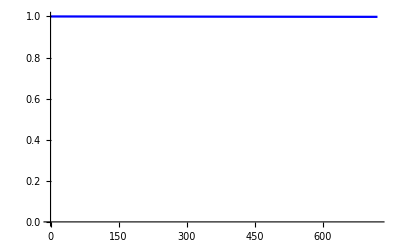

```mathematica
plot1m=ListLinePlot[prob1movr2y, PlotStyle->Blue, PlotRange->{0,1}]
```

```mathematica
probnoreinf3mtimecourse=Take[sarscov2probnoreinfectiontimecourse,90];
probnoreinf3m=Part[sarscov2probnoreinfectiontimecourse, 90];
prob3movr6y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,23]];
prob3movr2y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,7]];
```

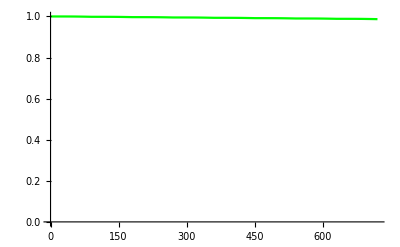

```mathematica
plot3m=ListLinePlot[prob3movr2y, PlotStyle->Green, PlotRange->{0,1}]
```

```mathematica
probnoreinf6mtimecourse=Take[sarscov2probnoreinfectiontimecourse,183];
probnoreinf6m=Part[sarscov2probnoreinfectiontimecourse, 183];
prob6movr6y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,11]];
prob6movr2y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,3]];
```

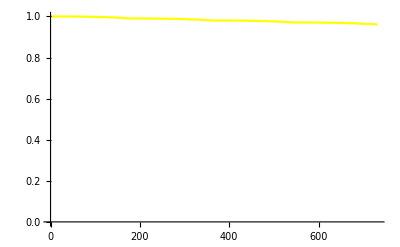

```mathematica
plot6m=ListLinePlot[prob6movr2y, PlotStyle->Yellow, PlotRange->{0,1}]
```

```mathematica
probnoreinf1ytimecourse=Take[sarscov2probnoreinfectiontimecourse,365];
probnoreinf1y=Part[sarscov2probnoreinfectiontimecourse, 365];
prob1yovr6y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,5]];
prob1yovr2y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,1]];
```

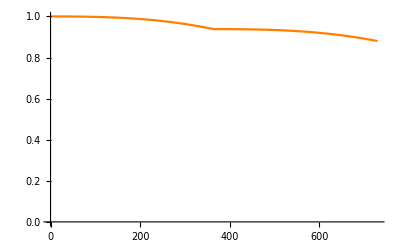

```mathematica
plot1y=ListLinePlot[prob1yovr2y, PlotStyle->Orange, PlotRange->{0,1}]
```

```mathematica
probnoreinf2ytimecourse=Take[sarscov2probnoreinfectiontimecourse,730];
probnoreinf2y=Part[sarscov2probnoreinfectiontimecourse, 730];
prob2yovr6y=Catenate[NestList[#*probnoreinf2y&,probnoreinf2ytimecourse,2]];
prob2yovr2y=Take[sarscov2probnoreinfectiontimecourse,730];
```

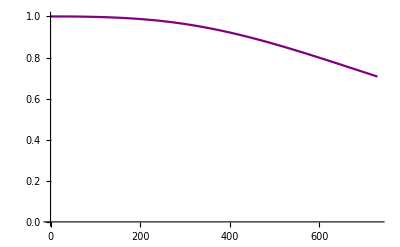

```mathematica
plot2y=ListLinePlot[prob2yovr2y, PlotStyle->Purple, PlotRange->{0,1}]
```

```mathematica
probnoreinf6ytimecourse=Take[sarscov2probnoreinfectiontimecourse,2190];
```

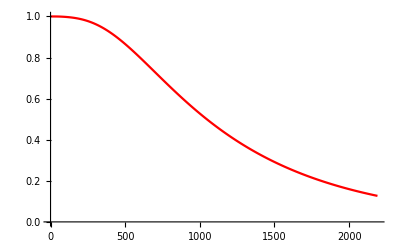

```mathematica
plot6y=ListLinePlot[probnoreinf6ytimecourse, PlotStyle->Red, PlotRange->{0,1}]
```

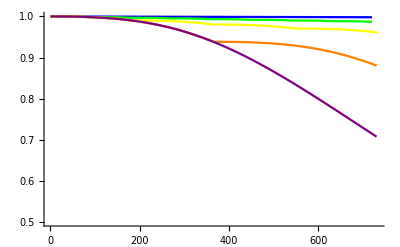

```mathematica
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1}]
```

```mathematica
Export[
StringJoin["/Users/hayley/Documents/townsend/spring-23/cancer/figs/targeted_hormonal_boosterovrtime-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

```mathematica
"/Users/hayley/Documents/townsend/spring-23/cancer/figs/targeted_hormonal_boosterovrtime-by-Day_04May2023.pdf"
```

```mathematica
Show[1-Last[prob2yovr2y], 1-Last[prob1yovr2y], 1-Last[prob6movr2y], 1-Last[prob3movr2y],1-Last[prob1movr2y]]
```

Show::gcomb: Could not combine the graphics objects in Show[0.292682,0.119599,0.0390544,0.0131032,0.00190911].

Show[0.292682,0.119599,0.0390544,0.0131032,0.00190911]

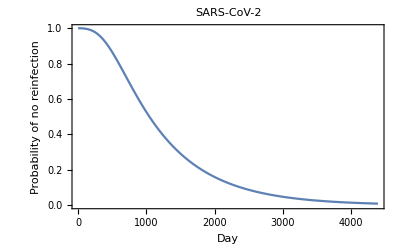

```mathematica
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
Export[
StringJoin["/Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_04May2023.pdf.

$Failed

```mathematica
sarscov2continuousprobnoreinfection=Interpolation[sarscov2probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{10.7392,0.357973,0.0294225}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1046.3,34.8767,2.86658}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{2957.4,98.58,8.10246}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov2probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov2probreinfectiondensity, 
If[day<1201,
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day]]]*sarscov2probnoreinfectiontimecourse[[day]],
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]]*sarscov2probnoreinfectiontimecourse[[day]]
]
]
];
```

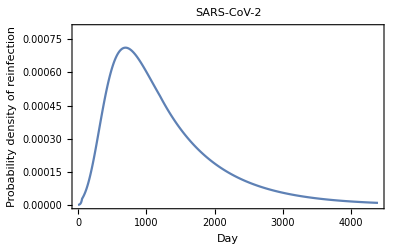

```mathematica
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0008},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0005},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_04May2023.pdf.

$Failed